# Mathematica Crash Course

### Designed for students with no Mathematica background, particularly those in Physics 361 and 363.

## Getting Started: Basic Functions and Operations

```mathematica
Clear["Global`*"] (* clear all variables in session-- important especially if your code isn't working! *)
```

Special Characters, Defining Variables and Functions (syntax)

Defining Variables and Special Characters: 
- start variable names with a lower case letter
- don’t use underscores in variable names
- to make a Greek letter, for example σ, hit `escape` sigma `escape` and capitalize Sigma to make Σ.

```mathematica
var1 = 1.0; (* semicolon supresses output *)
α = 7.0
β = α-var1
```

7.

6.

Functions: Mathematica’s and defining your own

All Mathematica functions begin with a capital letter and use square brackets [ ] for arguments. These can be things like Sin[x], ArcTan[x], Exp[x], etcetera

Forgot what a function needs as input? Hover over it.
- The blue “i” circle to show the help menu: Do it! It’s worth it! Every time!
- The arrows show a very brief summary of the help menu.

Your own functions:
- Don’t ask questions, just always put an underscore after the variable and use := rather than =

```mathematica
f[x_]:= Sin[x];
g[x_]:= x^5; (* hit `control` ^ to make an exponent *)
h[x_,y_]:= Sin[x*y] + y^2;
```

```mathematica
w[x_]:=x^2-2;
FindRoot[w[x],{x,-1.0}]
FindMinimum[w[x],x]
```

{x→-1.41421}

{-2.,{x→0.}}

Derivatives (and replacement rule)

```mathematica
D[f[x],x]/.x-> π (* evaluates derivative at some value *)
Derivative[0,1][h][x,y]
g'[x]
g''[x]
g'''[x]/.x-> 2.0  (* /. replaces variable with value! *)
```

-1

2 y+x Cos[x y]

5 x^4

20 x^3

240.

```mathematica
(* Replace multiple things at once!!!!!!!!!!! *)
a+b+c /. {a-> 1,b-> 2, c->99}
```

102

Integrals

```mathematica
Integrate[f[x],x] (* indefinite *)
Integrate[f[x],{x,0,π}] (* definite *)
Integrate[h[x,y],{x,0,π},{y,0,1}] (* exact integral *)
NIntegrate[h[x,y],{x,0,π},{y,0,1}] (* numerical approximation *)
```

-Cos[x]

2

EulerGamma+π/3-CosIntegral[π]+Log[π]

2.69548

Algebra Manipulation

```mathematica
Simplify[a*b*c/a+b + b*a/c] (* try FullSimplify if your result is not satisfactory *)

Solve[a^2+2*a*b+4 == c, b] (* make sure to hit `space` after double equal to make the symbol *)(* can input either numbers or UNDEFINED variables *)
(* run Clear[a,b,c] if you previously stored values in those variables *)

NSolve[4*x^4+5*x^5-2== 7]  (* gives numerical solutions, not exact *)
```

b (1+a/c+c)

{{b→(-4-a^2+c)/(2 a)}}

{{x→-1.10936-0.618548 ⅈ},{x→-1.10936+0.618548 ⅈ},{x→0.209359-1.03533 ⅈ},{x→0.209359+1.03533 ⅈ},{x→1.}}

## Matrices

Two methods:
1. Use curly brackets to create matrix, nest curly brackets for each row.
2. Go to Insert tab, select Table/Matrix and size then type in your numbers to blanks.

```mathematica
z={{1,2,3,0},{99,99,99,0},{7,8,9,0},{0,0,0,1}}
z//MatrixForm
MatrixForm[z]
```

{{1,2,3,0},{99,99,99,0},{7,8,9,0},{0,0,0,1}}

(1 | 2 | 3 | 0
99 | 99 | 99 | 0
7 | 8 | 9 | 0
0 | 0 | 0 | 1)

(1 | 2 | 3 | 0
99 | 99 | 99 | 0
7 | 8 | 9 | 0
0 | 0 | 0 | 1)

```mathematica
a=({{0, 0, 0}, {0, 2, 0}, {0, 0, 1}});
b=({{1}, {1}, {1}});
c=a.b;   (* use the dot . not the star * for matrix multiplication *)
MatrixForm[c]
```

(0
2
1)

## Plots

There are many different plotting commands that can be used: Plot, 3DPlot, ParametricPlot, ListPlot, etc.
The online documentation is good if you need something specific.

### Simple 2-D Plots

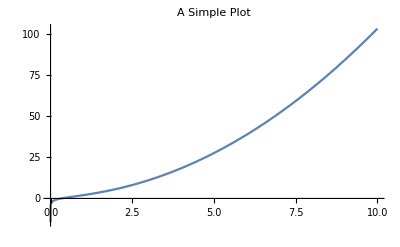

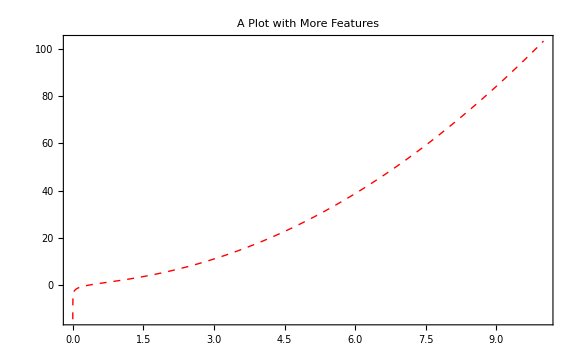

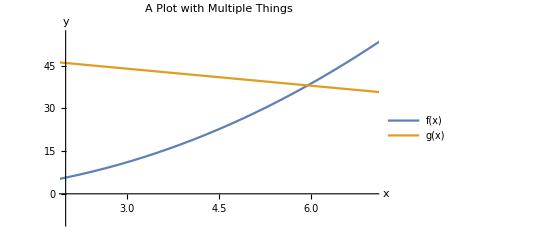

```mathematica
f[x_] :=1+x^2+Log[x]  
g[x_]:=50-2x
(* to construct arrow, use hyphen - and greater than > *)
Plot[f[x],{x,0,10},PlotLabel -> "A Simple Plot"]
Plot[f[x],{x,0,10},PlotLabel -> "A Plot with More Features", PlotStyle->{Red, Dashed, Thick},Frame-> True,ImageSize-> Large]
Plot[{f[x],g[x]},{x,0,10},PlotLabel -> "A Plot with Multiple Things",PlotLegends->"Expressions",AxesLabel-> {"x","y"},PlotRange->{{2,7},{-10,56}}]
```

```mathematica
Manipulate[Plot[{Sin[n*x],Sin[m*x]},{x,0,10}],{n,0,5},{m,1,6}]
```

### Parameterized Plots

The rules and commands for titles and labels are the same as they are for regular plotting.

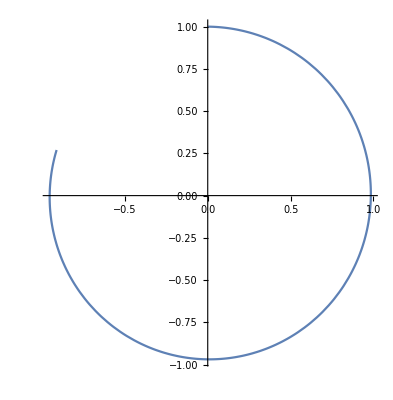

```mathematica
ParametricPlot[{Exp[-x/100]*Sin[x],Exp[-x/100]*Cos[x]},{x,0,5}]
```

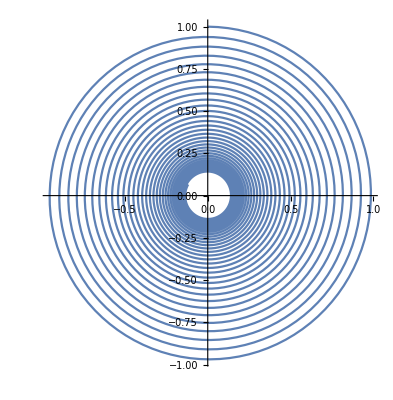

```mathematica
ParametricPlot[{Exp[-x/100]*Sin[x],Exp[-x/100]*Cos[x]},{x,0,200}]
```

#### Plotting Discrete Points and Creating Lists

You can create lists of numbers defined by a function using Tables.

```mathematica
numlist = Table[2n+5,{n,0,10}]
pairlist=Table[{n,n^2},{n,0,10}]
numlist[[1]] (* add extra brackets to pick out individual values*)
pairlist[[8,2]]
```

{5,7,9,11,13,15,17,19,21,23,25}

{{0,0},{1,1},{2,4},{3,9},{4,16},{5,25},{6,36},{7,49},{8,64},{9,81},{10,100}}

5

49

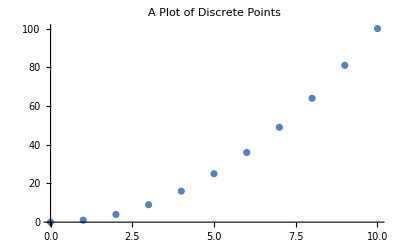

```mathematica
ListPlot[pairlist,PlotLabel->"A Plot of Discrete Points"]
```

#### 3D Plotting

Click and drag to move display angle.

```mathematica
Plot3D[Sin[x]+Sin[y],{x,0,Pi},{y,0,2Pi},PlotLabel->{"x","y","z"}]
Plot3D[x^2+y^2,{x,-10,10},{y,-10,10}]
```

-Graphics3D-

-Graphics3D-

## Loops

Do loops are used to repeatedly run something, print results, or evaluate expressions.

```mathematica
Do[Print[x],{x,1,2,0.25}]
```

1.

1.25

1.5

1.75

2.

```mathematica
Nest[Function[t,1/(1+t)],x,5]
```

1/(1+1/(1+1/(1+1/(1+1/(1+x)))))

You can also use While or For loops.

```mathematica
n=1;
n=n+1
i=1;
i++ (* this shorthand is useful for modifying loop structure, so n=n+1 same as n++ *)
i
```

2

1

2

```mathematica
For[n=1,n<4,n++,Print[x^n] ]
```

x

x^2

x^3

To modify a list and restore the results, use &/@ your_list_here command.

```mathematica
list=Table[{n,n^2},{n,1,10}]
{#[[1]],#[[2]]*2}&/@list
```

{{1,1},{2,4},{3,9},{4,16},{5,25},{6,36},{7,49},{8,64},{9,81},{10,100}}

{{1,2},{2,8},{3,18},{4,32},{5,50},{6,72},{7,98},{8,128},{9,162},{10,200}}

Refer to items in a list

```mathematica
onelinelist = Table[n+3,{n,3,13}];
matrixlist=Table[{n,n^2},{n,1,10}];
a=onelinelist[[3]]
b1=matrixlist[[5]][[1]]
b2 = matrixlist[[5,1]]   (* same as b1 *)
```

8

5

5

# Help Files

You can always go to the “Help” tab or while typing select the “i” for more information on an operator and its options.